```mathematica
FullSimplify[LogLikelihood[NormalDistribution[mu1,sigma1],{x1,x2,x3}]]
```

-1/(2 sigma1^2)(3 mu1^2+x1^2+x2^2+x3^2-2 mu1 (x1+x2+x3)+3 sigma1^2 Log[2 π])-3 Log[sigma1]

```mathematica
LogLikelihood[MixtureDistribution[{w1,w2},{NormalDistribution[mu1,sigma1],NormalDistribution[mu2,sigma2]}],{x1,x2,x3,x4}]
```

Log[(ⅇ^(-(-mu1+x1)^2/(2 sigma1^2)) w1)/(√(2 π) sigma1 (w1+w2))+(ⅇ^(-(-mu2+x1)^2/(2 sigma2^2)) w2)/(√(2 π) sigma2 (w1+w2))]+Log[(ⅇ^(-(-mu1+x2)^2/(2 sigma1^2)) w1)/(√(2 π) sigma1 (w1+w2))+(ⅇ^(-(-mu2+x2)^2/(2 sigma2^2)) w2)/(√(2 π) sigma2 (w1+w2))]+Log[(ⅇ^(-(-mu1+x3)^2/(2 sigma1^2)) w1)/(√(2 π) sigma1 (w1+w2))+(ⅇ^(-(-mu2+x3)^2/(2 sigma2^2)) w2)/(√(2 π) sigma2 (w1+w2))]+Log[(ⅇ^(-(-mu1+x4)^2/(2 sigma1^2)) w1)/(√(2 π) sigma1 (w1+w2))+(ⅇ^(-(-mu2+x4)^2/(2 sigma2^2)) w2)/(√(2 π) sigma2 (w1+w2))]

```mathematica
∑_(i=1)^n Log[(ⅇ^(-(-mu1+x[i])^2/(2 sigma1^2)) w1)/(√(2 π) sigma1 (w1+w2))+(ⅇ^(-(-mu2+x[i])^2/(2 sigma2^2)) w2)/(√(2 π) sigma2 (w1+w2))]
```

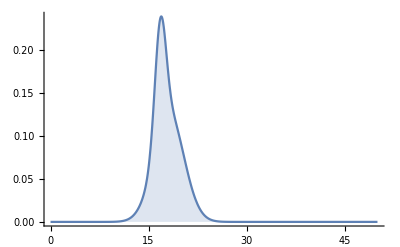

```mathematica
Plot[PDF[MixtureDistribution[{w1,w2},{NormalDistribution[mu1,sigma1],NormalDistribution[mu2,sigma2]}],x]/.{w1->0.276,w2->0.724,mu1->16.8,mu2->18.11,sigma1->Sqrt[0.715],sigma2->Sqrt[5.26]},{x,0,50},Filling->Bottom,PlotRange->All]
```